# Initialisation

```mathematica
Subscript[Y, ℓ_][θ_]=SphericalHarmonicY[ℓ,0,θ,ϕ];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,mathpazo,xcolor,bm,mhchem}","\\definecolor{darkgreen}{RGB}{0, 180, 0}"}];
```

# Spherium: RHF, UHF and symmetry breaking

The general function for the Hartree-Fock energy is:

```mathematica
EHF[R_,λ_]=∑_(L=0)^1 Subscript[a, L]^2(L(L+1))/(2 R^2)+∑_(L=0)^1 Subscript[b, L]^2(L(L+1))/(2 R^2)+∑_(i=0)^1 ∑_(j=0)^1 ∑_(k=0)^1 ∑_(l=0)^1 Subscript[a, i] Subscript[a, j] Subscript[b, k] Subscript[b, l] λ/R √((2i+1)(2j+1)(2k+1)(2l+1))∑_(L=0)^2 ThreeJSymbol[{i,0},{j,0},{L,0}]^2 ThreeJSymbol[{k,0},{l,0},{L,0}]^2/.{Subscript[a, 0]->Cos[x],Subscript[a, 1]->Sin[x],Subscript[b, 0]->Cos[y],Subscript[b, 1]->Sin[y]};
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{1,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{2,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

We search stationnary solution

```mathematica
sol=Solve[{D[EHF[R,1], x]==0,D[EHF[R,1], y]==0},{x,y}]/.{C[1]->0,C[2]->0}//FullSimplify
```

{{x→0,y→0},{x→0,y→-π/2},{x→0,y→π/2},{x→0,y→π},{x→-π/2,y→0},{x→-π/2,y→-π/2},{x→-π/2,y→π/2},{x→-π/2,y→π},{x→π/2,y→0},{x→π/2,y→-π/2},{x→π/2,y→π/2},{x→π/2,y→π},{x→π,y→0},{x→π,y→-π/2},{x→π,y→π/2},{x→π,y→π},{x→ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y→ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x→ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y→ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x→ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y→ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x→ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y→ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x→ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y→ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x→ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y→ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x→ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y→ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x→ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y→ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x→ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y→ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x→ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y→ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]},{x→ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y→ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]},{x→ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y→ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x→ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y→ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]},{x→ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y→ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x→ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y→ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x→ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y→ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]}}

Some solutions correspond to RHF solutions et some to UHF solutions.

```mathematica
solRHF={{x->0,y->0},{x->0,y->π},{x->-π/2,y->-π/2},{x->-π/2,y->π/2},{x->π/2,y->-π/2},{x->π/2,y->π/2},{x->π,y->0},{x->π,y->π},{x->ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y->ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x->ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x->ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y->ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x->ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y->ArcTan[-(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]},{x->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y->ArcTan[-(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]},{x->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)],y->ArcTan[(√(-75+38 R))/(√R),(5 √(3+2 R))/(√R)]}};
```

```mathematica
solUHF={{x->0,y->-π/2},{x->0,y->π/2},{x->-π/2,y->0},{x->-π/2,y->π},{x->π/2,y->0},{x->π/2,y->π},{x->π,y->-π/2},{x->π,y->π/2},{x->ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y->ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x->ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y->ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]},{x->ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y->ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]},{x->ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y->ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x->ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y->ArcTan[-(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]},{x->ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)],y->ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x->ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y->ArcTan[-(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)]},{x->ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y->ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]}};
```

The two electrons integrals are equal to

```mathematica
Subscript[U, i_,j_,k_,l_]:=√((2i+1)(2j+1)(2k+1)(2l+1))∑_(L=0)^2 ThreeJSymbol[{i,0},{j,0},{L,0}]^2 ThreeJSymbol[{k,0},{l,0},{L,0}]^2;
```

The Fock operator for the electron α is

```mathematica
Fα=Table[KroneckerDelta[i,j](i(i+1))/(2 R^2)+λ/R∑_(k=0)^1 ∑_(l=0)^1 Subscript[a, k] Subscript[a, l](Subscript[U, i,j,k,l]-Subscript[U, i,l,k,j])+λ/R∑_(k=0)^1 ∑_(l=0)^1 Subscript[b, k] Subscript[b, l](Subscript[U, i,j,k,l])/.{Subscript[a, 0]->Cos[x],Subscript[a, 1]->Sin[x],Subscript[b, 0]->Cos[y],Subscript[b, 1]->Sin[y]}/.λ->1//FullSimplify//Expand,{i,0,1},{j,0,1}]
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{1,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{2,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

{{4/(3 R)-Cos[2 x]/(3 R),-Sin[2 x]/(3 R)+Sin[2 y]/(3 R)},{-Sin[2 x]/(3 R)+Sin[2 y]/(3 R),1/R^2+106/(75 R)+Cos[2 x]/(3 R)-(2 Cos[2 y])/(25 R)}}

And the Fock operator β

```mathematica
Fβ=Table[KroneckerDelta[i,j](i(i+1))/(2 R^2)+λ/R∑_(k=0)^1 ∑_(l=0)^1 Subscript[b, k] Subscript[b, l](Subscript[U, i,j,k,l]-Subscript[U, i,l,k,j])+λ/R∑_(k=0)^1 ∑_(l=0)^1 Subscript[a, k] Subscript[a, l](Subscript[U, i,j,k,l])/.{Subscript[a, 0]->Cos[x],Subscript[a, 1]->Sin[x],Subscript[b, 0]->Cos[y],Subscript[b, 1]->Sin[y]}/.λ->1//FullSimplify//Expand,{i,0,1},{j,0,1}]
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{1,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{0,0},{2,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

{{4/(3 R)-Cos[2 y]/(3 R),Sin[2 x]/(3 R)-Sin[2 y]/(3 R)},{Sin[2 x]/(3 R)-Sin[2 y]/(3 R),1/R^2+106/(75 R)-(2 Cos[2 x])/(25 R)+Cos[2 y]/(3 R)}}

## RHF solutions

In the RHF case Fα = Fβ

```mathematica
Fα/.solRHF//FullSimplify//Expand
```

{{{1/R,0},{0,1/R^2+5/(3 R)}},{{1/R,0},{0,1/R^2+5/(3 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{1/R,0},{0,1/R^2+5/(3 R)}},{{1/R,0},{0,1/R^2+5/(3 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}}}

```mathematica
Fβ/.solRHF//FullSimplify//Expand
```

{{{1/R,0},{0,1/R^2+5/(3 R)}},{{1/R,0},{0,1/R^2+5/(3 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{5/(3 R),0},{0,1/R^2+29/(25 R)}},{{1/R,0},{0,1/R^2+5/(3 R)}},{{1/R,0},{0,1/R^2+5/(3 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}},{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}}}

The 16 stationnary RHF solutions yields 3  differents Fockian which are all diagonal.

```mathematica
{{{1/R,0},{0,1/R^2+5/(3 R)}}//MatrixForm,{{5/(3 R),0},{0,1/R^2+29/(25 R)}}//MatrixForm,{{25/(44 R^2)+91/(66 R),0},{0,25/(44 R^2)+91/(66 R)}}//MatrixForm}
```

{(1/R | 0
0 | 1/R^2+5/(3 R)),(5/(3 R) | 0
0 | 1/R^2+29/(25 R)),(25/(44 R^2)+91/(66 R) | 0
0 | 25/(44 R^2)+91/(66 R))}

The first solution corresponds to a density matrix spatially symmetric where the two electrons are in Y_0 and the second to a density matrix spatially symmetric where the two electrons are in Y_1. The last solution corresponds to the symmetry broken RHF solution. In the sb-RHF solution the two orbitals are degenerate.

```mathematica
{D[EHF[R,1], x,x],D[EHF[R,1], y,y]}/.{{x->0,y->π},{x->π/2,y->-π/2},{x->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)],y->ArcTan[(√(-75+38 R))/(√R),-(5 √(3+2 R))/(√R)]}}//FullSimplify
```

{{2/R^2,2/R^2},{-(50+8 R)/(25 R^2),-(50+8 R)/(25 R^2)},{-4/(3 R),-4/(3 R)}}

```mathematica
Solve[-(50+8 R)/(25 R^2)==0,R]
```

{{R→-25/4}}

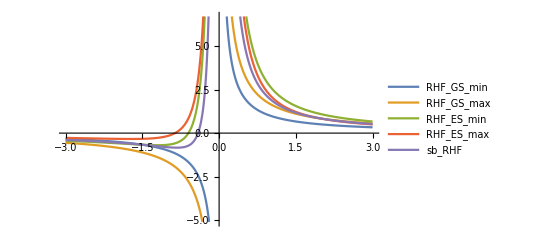

```mathematica
Plot[{1/R,5/(3R),1/R^2+5/(3 R),1/R^2+29/(25 R),25/(44 R^2)+91/(66 R)},{R,-3,3},PlotLegends->{"RHF_GS_min","RHF_GS_max","RHF_ES_min","RHF_ES_max","sb_RHF"}]
```

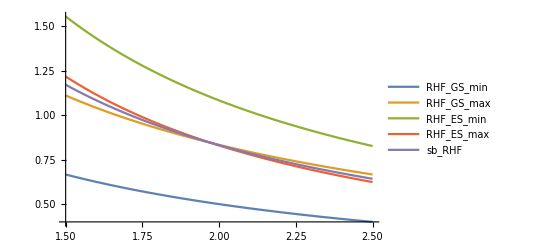

```mathematica
Plot[{1/R,5/(3R),1/R^2+5/(3 R),1/R^2+29/(25 R),25/(44 R^2)+91/(66 R)},{R,1.5,2.5},PlotLegends->{"RHF_GS_min","RHF_GS_max","RHF_ES_min","RHF_ES_max","sb_RHF"}]
```

```mathematica
Solve[5/(3 R)==1/R^2+29/(25 R),R]
```

{{R→75/38}}

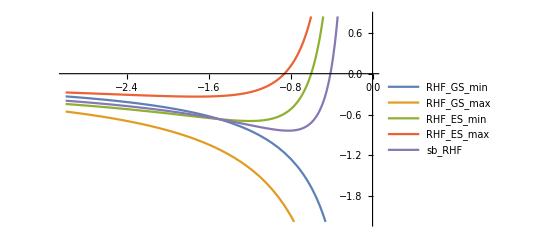

```mathematica
Plot[{1/R,5/(3R),1/R^2+5/(3 R),1/R^2+29/(25 R),25/(44 R^2)+91/(66 R)},{R,0,-3},PlotLegends->{"RHF_GS_min","RHF_GS_max","RHF_ES_min","RHF_ES_max","sb_RHF"}]
```

```mathematica
Solve[1/R==1/R^2+5/(3 R),R]
```

{{R→-3/2}}

The sb-RHF energy interacts with the minimized RHF for R<0 and the maximized RHF for R>0. For negative value of R there is a point at which the attraction of the sb-RHF will minimize the energy than the kinetical energy.  For positive value of lambda there is a point at which the repulsion of the sb RHF solution is bigger than the kinetical energy.

## UHF solutions

```mathematica
Fα/.solUHF//FullSimplify//Expand
```

{{{1/R,0},{0,1/R^2+137/(75 R)}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{5/(3 R),0},{0,1/R^2+1/R}},{{5/(3 R),0},{0,1/R^2+1/R}},{{5/(3 R),0},{0,1/R^2+1/R}},{{5/(3 R),0},{0,1/R^2+1/R}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}}}

```mathematica
Fβ/.solUHF//FullSimplify//Expand
```

{{{5/(3 R),0},{0,1/R^2+1/R}},{{5/(3 R),0},{0,1/R^2+1/R}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{1/R,0},{0,1/R^2+137/(75 R)}},{{5/(3 R),0},{0,1/R^2+1/R}},{{5/(3 R),0},{0,1/R^2+1/R}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),-(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{-(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}},{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}}}

The 16 stationnary UHF solutions yields 3  differents Fockian, only two of them are already diagonal.

```mathematica
{{{5/(3 R),0},{0,1/R^2+1/R}}//MatrixForm,{{1/R,0},{0,1/R^2+137/(75 R)}}//MatrixForm,DiagonalMatrix[{{-25/(56 R^2)+109/(84 R),(5 √(-3+2 R) √(75+62 R))/(84 R^2)},{(5 √(-3+2 R) √(75+62 R))/(84 R^2),75/(56 R^2)+121/(84 R)}}//Eigenvalues//Expand]//MatrixForm}
```

{(5/(3 R) | 0
0 | 1/R^2+1/R),(1/R | 0
0 | 1/R^2+137/(75 R)),(25/(56 R^2)+57/(28 R) | 0
0 | 25/(56 R^2)+59/(84 R))}

```mathematica
{D[EHF[R,1], x,x],D[EHF[R,1], y,y]}/.{{x->0,y->π/2},{x->-π/2,y->0},{x->ArcTan[(√(75+62 R))/(√R),(5 √(-3+2 R))/(√R)],y->ArcTan[(√(75+62 R))/(√R),-(5 √(-3+2 R))/(√R)]}}//FullSimplify
```

{{(50+8 R)/(25 R^2),-2/R^2},{-2/R^2,(50+8 R)/(25 R^2)},{4/(3 R),4/(3 R)}}

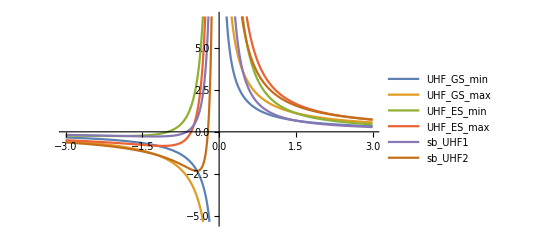

```mathematica
Plot[{1/R,5/(3R),1/R^2+1/R,1/R^2+137/(75 R),25/(56 R^2)+59/(84 R),25/(56 R^2)+57/(28 R)},{R,-3,3},PlotLegends->{"UHF_GS_min","UHF_GS_max","UHF_ES_min","UHF_ES_max","sb_UHF1","sb_UHF2"}]
```

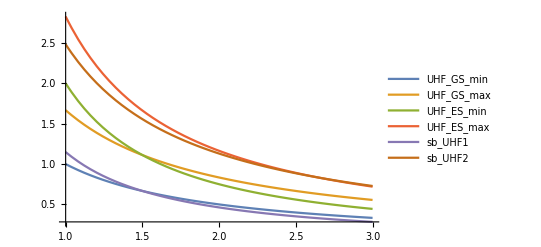

```mathematica
Plot[{1/R,5/(3R),1/R^2+1/R,1/R^2+137/(75 R),25/(56 R^2)+59/(84 R),25/(56 R^2)+57/(28 R)},{R,1,3},PlotLegends->{"UHF_GS_min","UHF_GS_max","UHF_ES_min","UHF_ES_max","sb_UHF1","sb_UHF2"}]
```

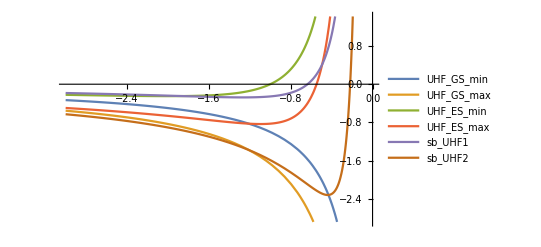

```mathematica
Plot[{1/R,5/(3R),1/R^2+1/R,1/R^2+137/(75 R),25/(56 R^2)+59/(84 R),25/(56 R^2)+57/(28 R)},{R,0,-3},PlotLegends->{"UHF_GS_min","UHF_GS_max","UHF_ES_min","UHF_ES_max","sb_UHF1","sb_UHF2"}]
```

For R>0 the sb-UHF solution is a minimum because the symmetry breaking minimize the repulsion and for R<0 this is a maximum because the symmetry breaking minimize the attraction.
For R>0 the sb-UHF 1 is the “bonding” solution and the sb-UHF 2 is the antibonding solution. There is a point a which the bonding solution becomes better than the ground state of the symmetric solution, and an other point at which the anti bonding solution becomes higher than the symetric solution.
We can do the same reasoning for R<0.

## sb-RHF and sb-UHF

```mathematica
Table[ EHF[R,1]/.sol⟦k⟧,{k,Length[sol]}]//FullSimplify//Expand//DeleteDuplicates
```

{1/R,1/R^2+1/R,2/R^2+29/(25 R),75/(88 R^3)+25/(22 R^2)+91/(66 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R)}

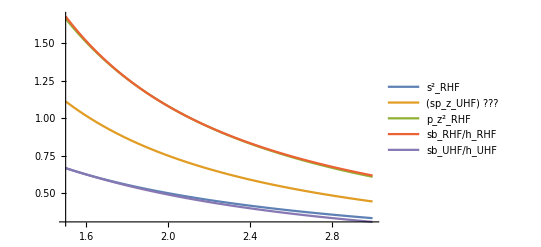

```mathematica
Plot[{1/R,1/R^2+1/R,2/R^2+29/(25 R),75/(88 R^3)+25/(22 R^2)+91/(66 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R)},{R,1.5,3},PlotLegends->{"s^2_RHF","(sp_z_UHF) ???","p_z^2_RHF","sb_RHF/h_RHF","sb_UHF/h_UHF"}]
```

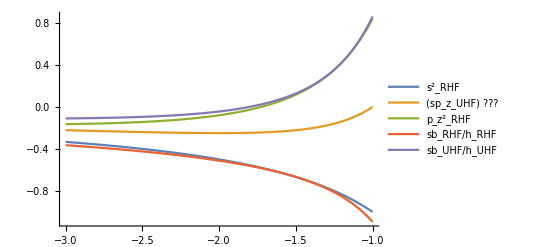

```mathematica
Plot[{1/R,1/R^2+1/R,2/R^2+29/(25 R),75/(88 R^3)+25/(22 R^2)+91/(66 R),-75/(112 R^3)+25/(28 R^2)+59/(84 R)},{R,-1,-3},PlotLegends->{"s^2_RHF","(sp_z_UHF) ???","p_z^2_RHF","sb_RHF/h_RHF","sb_UHF/h_UHF"}]
```

For R > 0:
-the sb_RHF solution is a maximum and exist for R>75/38 (~1.97) before it is a holomorphic solution
-the sb_UHF solution is a minimum and exist for R>3/2  before it is a holomorphic solution
For R<0:
-the sb_RHF solution is a minimum and exist for R<-3/2 after it is a holomorphic solution
-the sb_UHF solution is a maximum and exist for R<-75/62(~1.2) after it is a holomorphic solution

Those points are the Coulson-Fischer points of the sb-RHF and sb-UHF solutions.